# Choosing Best From 3 methods

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
$Path=Append[$Path,FileNames["*",{Directory[]<>"\1DPackage"}]];
```

Syntax::sntoct1: 3 octal digits are required after \ to construct an 8-bit character.

```mathematica
<<"pyramid1d`"
<<"pyramidalStereoAll`"
<<"pixelTest`"
<<"lineTest`"
```

## read

```mathematica
read[set_,num_,reduce_,corf_]:=Module[{ia,ib,id,rgb2d,reduire,clean,io,left,right,disp,occ, frame, base,fileleft,fileright},(

base="D:\MastersMathematica\Data\Sintel";

frame="frame_"<>num<>".png";
fileleft=corf<>"_left";
fileright=corf<>"_right";
left=FileNameJoin[{base,"training",fileleft,set,frame}];
right=FileNameJoin[{base,"training",fileright,set,frame}];
disp=FileNameJoin[{base,"training","disparities",set,frame}];
occ=FileNameJoin[{base,"training","occlusions",set,frame}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];
reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];
ia=reduire[ColorConvert[clean@Import[left],"GrayScale"],reduce];
ib=reduire[ColorConvert[clean@Import[right],"GrayScale"],reduce];
id=reduire[Image[
rgb2d[Flatten[N@ImageData[clean@Import[disp],"Byte"],{{3},{1},{2}}]]
],reduce]/reduce;
io=reduire[ColorConvert[clean@Import[occ],"GrayScale"],reduce];
read[{left,right,disp,occ},reduce]={ia,ib,id,io};

{ia,ib,id,io}
)];
```

## Test Design

```mathematica
(*Counts the amount of colors in solution*)
countColors[v_]:=Block[{count},
count=0;
ImageScan[If[Mean[#]≠0,count++]&,v];
count
]
```

```mathematica
(*Runs different tests {1,m}, {n,n}, {n,m}, {2,m+1}*)
(*Error is updated depending in the highest res level *)

testn=4;

test1[ia_,ib_,lvl_,e_,mode_]:=Block[{},(

Flatten[Table[
{stereoDepth[ia,ib,lvl,{i,lvl},e,mode],
stereoDepth[ia,ib,i,{i,i},e,mode],
stereoDepth[ia,ib,i,{1,i},e,mode],
stereoDepth[ia,ib,i,{2,i+1},e,mode]
}
,{i,lvl}],1]

)]
```

```mathematica
test2[ia_,ib_,{lvlmin_,lvlmax_},e_,mode_]:=Block[{},(
stereoDepth[ia,ib,lvlmax-1,{lvlmin,lvlmax},e,mode]
)]
```

```mathematica
(* Formats result  to show minMax in solution,disparity map, real solution, status map, Histogram, cero count and RMES *)

result1[t_,s_]:=Block[{minmaxid,flipMask,signMask,magMask,okMask,convergedMask,lst1,lst2,p,histogram,imageConverged,imageOk,imageFlip,imageSign,imageMag},(

minmaxid=MinMax[Flatten[ImageData[s]]];
(*seeStatus={"converged"->Transparent,"ok"->Transparent,"flip"->Red,"sign"->Purple,"mag"->Yellow};*)
flipMask={"converged"->Transparent,"ok"->Transparent,"flip"->Orange,"sign"->Transparent,"mag"->Transparent};
signMask={"converged"->Transparent,"ok"->Transparent,"flip"->Transparent,"sign"->Red,"mag"->Transparent};
magMask={"converged"->Transparent,"ok"->Transparent,"flip"->Transparent,"sign"->Transparent,"mag"->Purple};
okMask={"converged"->Transparent,"ok"->Pink,"flip"->Transparent,"sign"->Transparent,"mag"->Transparent};
convergedMask={"converged"->Green,"ok"->Transparent,"flip"->Transparent,"sign"->Transparent,"mag"->Transparent};

Table[
lst1=Flatten[-result[[All,All,1]]];
lst2=Flatten[ImageData[s]];

p=Flatten[Position[Flatten[result[[All,All,2]]],#]&/@{"sign","mag","flip","ok"},1];
lst1=Delete[lst1,p];
lst2=Delete[lst2,p];

histogram=Histogram[Clip[#&/@{lst1,lst2},{-1,50}],{0.1}];
histogram2=Histogram[Clip[#&/@{Flatten[-result[[All,All,1]]],Flatten[ImageData[s]]},{-1,50}],{0.1}];

imageConverged=Image[result[[All,All,2]]/.convergedMask];
imageOk=Image[result[[All,All,2]]/.okMask];
imageFlip=Image[result[[All,All,2]]/.flipMask];
imageSign=Image[result[[All,All,2]]/.signMask];
imageMag=Image[result[[All,All,2]]/.magMask];

{Image[-result[[All,All,1]]]/(minmaxid[[2]]),
s/(minmaxid[[2]]),
Grid[{{imageConverged},{countColors[imageConverged]}}],
Grid[{{imageOk},{countColors[imageOk]}}],
Grid[{{imageFlip},{countColors[imageFlip]}}],
Grid[{{imageSign},{countColors[imageSign]}}],
Grid[{{imageMag},{countColors[imageMag]}}],
countColors[imageFlip]+countColors[imageSign]+countColors[imageMag],
Show[histogram],
N@Sqrt[Mean[Power[lst1-lst2,2]]],
Show[histogram2],
N@Sqrt[Mean[Power[Flatten[-result[[All,All,1]]]-Flatten[ImageData[s]],2]]]
}

,{result,t}]

)]
```

## Data 1

```mathematica
d=1;

(* downscaling *)
r=2;
{ia,ib,id,io}=read["bamboo_1","0001",r,"clean"]

MinMax[id]

(* a reduction of 6 is {173,73} *)
(*{ia,ib,id,io}=ImageCrop[#,{173,73}]&/@{ia,ib,id,io}*)

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=150/r;
ny=300/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}
ic=move[ia,-7];
max=MinMax[Flatten[ImageData[id]]][[2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{0.136895,38.6009}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45},{103,45}}

12.5952

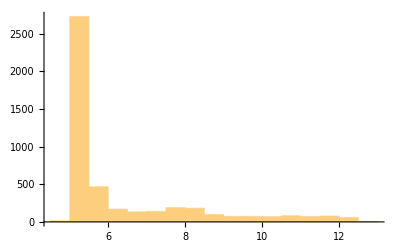

{4.70419,12.5952}

```mathematica
Histogram[Flatten[ImageData[id]]]
minmaxid=MinMax[Flatten[ImageData[id]]]
```

## Results

Sign methods, increase the flip error and mag error due to the proximity to cero.

### OverConstrained

“OverConstrained” is a model which will move from lowest resolution to highest
One scale reject is enough to make that solution undefined and then defined as cero

Attention: Highest resolution can reject all the chain of solutions.
More results appear by lowering the resolution of the pyramid’s base. The smoother shape allows more solutions.
maintaining the resolution of the base will calculate more results in a slow pase due to the assistance of previous good values.

```mathematica
d=1;
e=0.001;
mode="OverConstrained";
```

```mathematica
(* ia, ib, number of lvls, error, mode *)
Subscript[test^mode, d]=test1[ia,ic,6,e, mode];
Dimensions[Subscript[test^mode, d]]
```

{24,45,103,4}

```mathematica
(* Will result on a grid containing -> {reusult, real values, converged map, Ok, Flip, Sign, Mag, tot errors, defined Hist, defined RMSE, All Hist, All RMSE} *)
Subscript[result^mode, d]=result1[Subscript[test^mode, d],id];
```

```mathematica
Dimensions[Subscript[result^mode, d]]
```

{24,12}

```mathematica
(* testn is the amount of tests function test1 is doing *)
Subscript[resultTest^mode, d]=Table[Partition[Subscript[result^mode, d],testn][[All,p]],{p,testn}];
```

```mathematica
columnName={"x","y","Converged","Ok","Flip","Sign","Mag","Errors","Histogram","RMSE","HistogramTot","RMSETot"};
```

```mathematica
(* m different grids to display results *)
Subscript[gridRt^mode, d]=Table[Grid[Prepend[rt,columnName],Frame->All],{rt,Subscript[resultTest^mode, d]}];
```

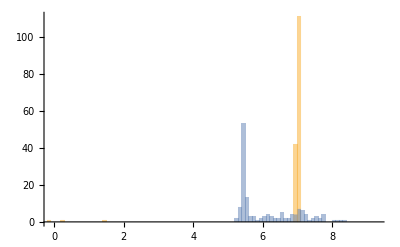
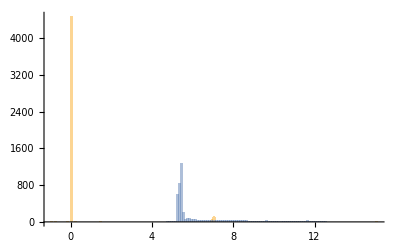
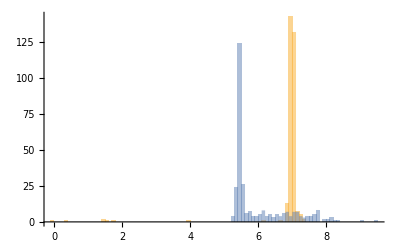
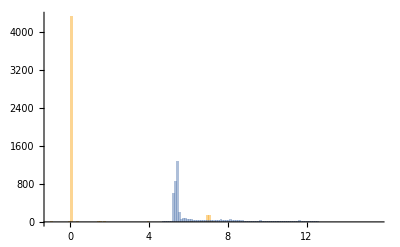
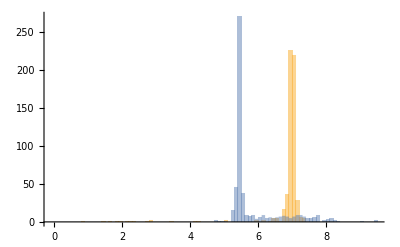
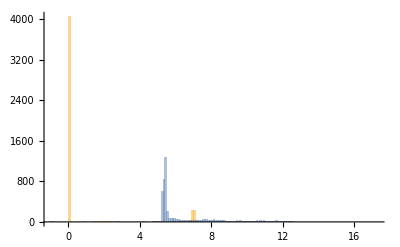
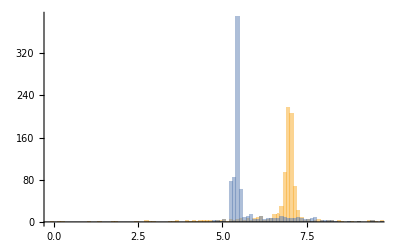
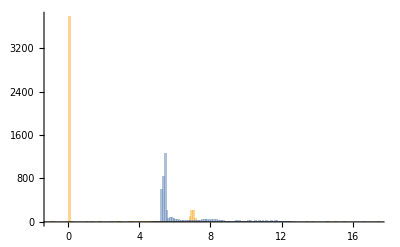
x | y | Converged | Ok | Flip | Sign | Mag | Errors | Histogram | RMSE | HistogramTot | RMSETot
-Graphics- | -Graphics- | -Graphics-
160 | -Graphics-
1 | -Graphics-
1259 | -Graphics-
3060 | -Graphics-
155 | 4474 | -Graphics- | 3.4681 | -Graphics- | 6.56869
-Graphics- | -Graphics- | -Graphics-
317 | -Graphics-
0 | -Graphics-
1048 | -Graphics-
2982 | -Graphics-
288 | 4318 | -Graphics- | 3.42369 | -Graphics- | 6.50171
-Graphics- | -Graphics- | -Graphics-
579 | -Graphics-
0 | -Graphics-
717 | -Graphics-
2809 | -Graphics-
530 | 4056 | -Graphics- | 2.44875 | -Graphics- | 6.31566
-Graphics- | -Graphics- | -Graphics-
851 | -Graphics-
0 | -Graphics-
299 | -Graphics-
2572 | -Graphics-
913 | 3784 | -Graphics- | 3.50361 | -Graphics- | 6.27977
-Graphics- | -Graphics- | -Graphics-
1029 | -Graphics-
0 | -Graphics-
14 | -Graphics-
2191 | -Graphics-
1401 | 3606 | -Graphics- | 3.54172 | -Graphics- | 6.16319
-Graphics- | -Graphics- | -Graphics-
1237 | -Graphics-
0 | -Graphics-
0 | -Graphics-
1795 | -Graphics-
1603 | 3398 | -Graphics- | 11.5321 | -Graphics- | 8.12856

```mathematica
(* Ploting all Errors and RMSE from test 1, n different scales *)
ntest=1;
mode="OverConstrained";
d=1;
Subscript[gridRt^mode, d][[ntest]]
```

#### Tests

```mathematica
row=14;
lvls=5;
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvls];
pyrfib=pyrFuncGen[ImageData[ic][[row]], lvls];

pyrfi=Flatten[{pyrfia,pyrfib},{{2},{1},{3}}];
```

```mathematica
lvlmin=5;
lvlmax=6;
```

```mathematica
Image[-test2[ia,ib,{lvlmin,lvlmax},e,mode][[All,All,1]]]/max
```

-Graphics-

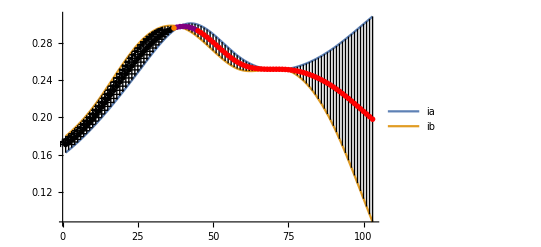

```mathematica
lineTest[Range[ImageDimensions[ia][[1]]],{lvlmin,lvlmax},pyrfi,e,mode]
```

```mathematica
ListAnimate[pixelTest[20,15,6,pyrfi[[5;;6]],e,mode]]
```

### SemiConstrained

“SemiConstrained” is a model which will move from lowest resolution to highest

One scale reject continues holding up the last acceptable solution

Note: To continue means that a good solution might be lost in the middle of the next scale iteration, and solution ends up not making sense

Possible solution: Replace {v1, v2} only if converged.

maintaining the resolution of the base will calculate more results in a slow pase due to the assistance of previous good values.

```mathematica
d=1;

mode="SemiConstrained";
```

```mathematica
Subscript[test^mode, d]=test1[ia,ic,6,e, mode];
Dimensions[Subscript[test^mode, d]]
```

{24,45,103,4}

```mathematica
Subscript[result^mode, d]=result1[Subscript[test^mode, d],id];
```

```mathematica
Dimensions[Subscript[result^mode, d]]
```

{24,12}

```mathematica
(* testn is the amount of tests function test1 is doing *)
Subscript[resultTest^mode, d]=Table[Partition[Subscript[result^mode, d],testn][[All,p]],{p,testn}];
```

```mathematica
Dimensions[Subscript[result^mode, d][[1]]]
```

{12}

```mathematica
columnName={"x","y","Converged","Ok","Flip","Sign","Mag","Errors","Histogram","RMSE"};
```

```mathematica
(* m different grids to display results *)
Subscript[gridRt^mode, d]=Table[Grid[Prepend[rt,columnName],Frame->All],{rt,Subscript[resultTest^mode, d]}];
```

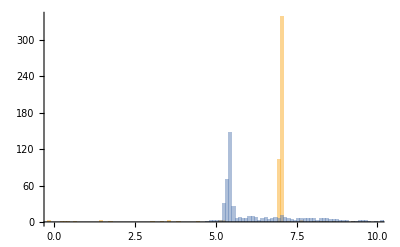
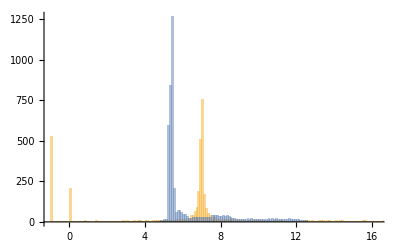
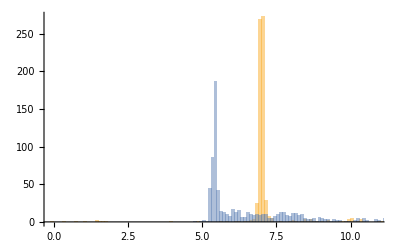
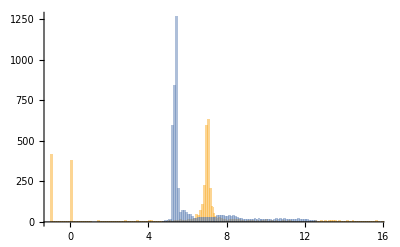
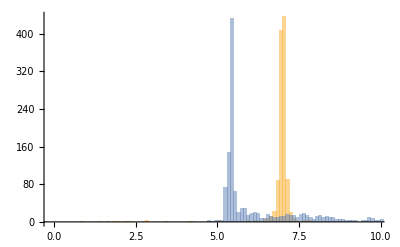
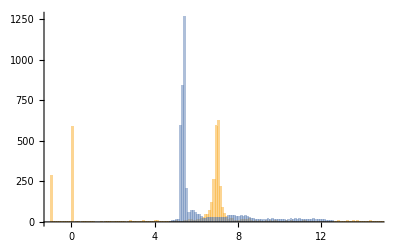
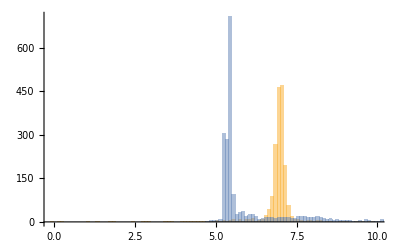
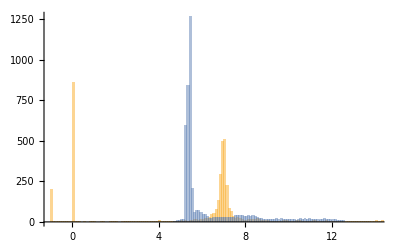
x | y | Converged | Ok | Flip | Sign | Mag | Errors | Histogram | RMSE |  | 
-Graphics- | -Graphics- | -Graphics-
536 | -Graphics-
22 | -Graphics-
2200 | -Graphics-
1783 | -Graphics-
94 | 4077 | -Graphics- | 10.3469 | -Graphics- | 35.9853
-Graphics- | -Graphics- | -Graphics-
741 | -Graphics-
7 | -Graphics-
2049 | -Graphics-
1666 | -Graphics-
172 | 3887 | -Graphics- | 10.5521 | -Graphics- | 28.9709
-Graphics- | -Graphics- | -Graphics-
1278 | -Graphics-
2 | -Graphics-
1429 | -Graphics-
1678 | -Graphics-
248 | 3355 | -Graphics- | 9.14234 | -Graphics- | 20.8676
-Graphics- | -Graphics- | -Graphics-
2075 | -Graphics-
0 | -Graphics-
528 | -Graphics-
1606 | -Graphics-
426 | 2560 | -Graphics- | 8.33062 | -Graphics- | 14.8218
-Graphics- | -Graphics- | -Graphics-
1699 | -Graphics-
0 | -Graphics-
17 | -Graphics-
1761 | -Graphics-
1158 | 2936 | -Graphics- | 7.87944 | -Graphics- | 14.4505
-Graphics- | -Graphics- | -Graphics-
1237 | -Graphics-
0 | -Graphics-
0 | -Graphics-
1795 | -Graphics-
1603 | 3398 | -Graphics- | 11.5321 | -Graphics- | 10.6183

```mathematica
(* Ploting all Errors and RMSE from test 1, n different scales *)
ntest=1;
mode="SemiConstrained";
d=1;
Subscript[gridRt^mode, d][[ntest]]
```

#### Tests

```mathematica
row=3;
lvls=5;
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvls];
pyrfib=pyrFuncGen[ImageData[ic][[row]], lvls];

pyrfi=Flatten[{pyrfia,pyrfib},{{2},{1},{3}}];
```

```mathematica
lvlmin=5;
lvlmax=6;
```

```mathematica
Image[-test2[ia,ib,{lvlmin,lvlmax},e,mode][[All,All,1]]]/max
```

-Graphics-

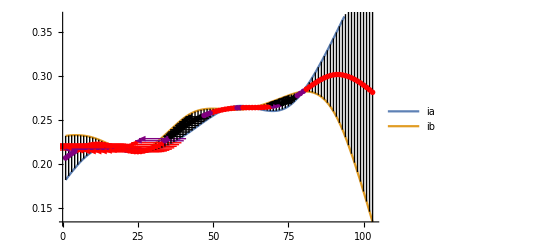

```mathematica
lineTest[Range[ImageDimensions[ia][[1]]],{lvlmin,lvlmax},pyrfi,e,mode]
```

```mathematica
p=20;
ListAnimate[pixelTest[p,20,6,pyrfi[[5;;6]],e,mode]]
```

### Constrained

“Constrained” is a model which will move from lowest resolution to highest
Two scale reject is enough to make that solution undefined and then defined as cero

```mathematica
d=1;

mode="Constrained";
```

```mathematica
Subscript[test^mode, d]=test1[ia,ib,6,0.01, mode];
Dimensions[Subscript[test^mode, d]]
```

{24,45,103,4}

```mathematica
Subscript[result^mode, d]=result1[Subscript[test^mode, d],id];
```

```mathematica
Dimensions[Subscript[result^mode, d]]
```

{24,12}

```mathematica
(* testn is the amount of tests function test1 is doing *)
Subscript[resultTest^mode, d]=Table[Partition[Subscript[result^mode, d],testn][[All,p]],{p,testn}];
```

```mathematica
Dimensions[Subscript[result^mode, d][[1]]]
```

{12}

```mathematica
columnName={"x","y","Converged","Ok","Flip","Sign","Mag","Errors","Histogram","RMSE"};
```

```mathematica
(* m different grids to display results *)
Subscript[gridRt^mode, d]=Table[Grid[Prepend[rt,columnName],Frame->All],{rt,Subscript[resultTest^mode, d]}];
```

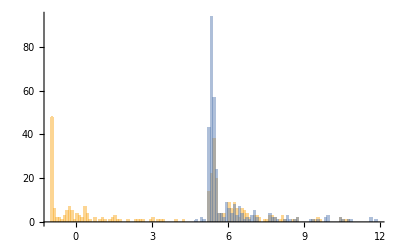
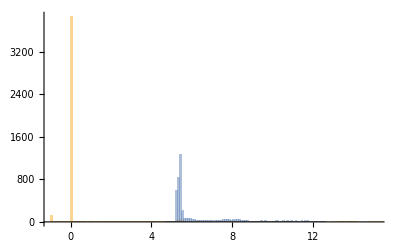
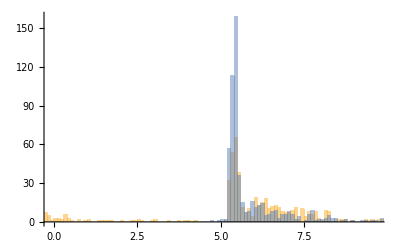
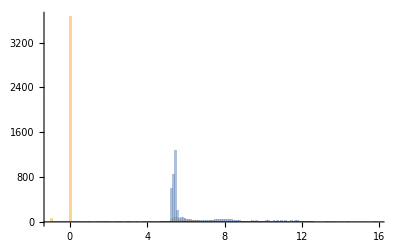
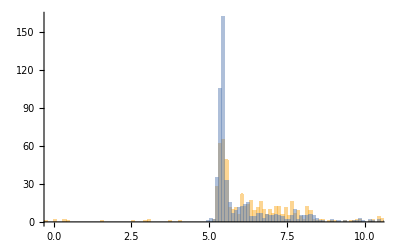
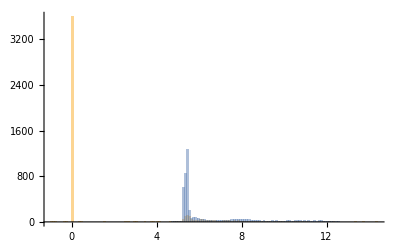
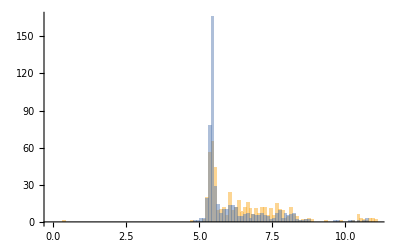
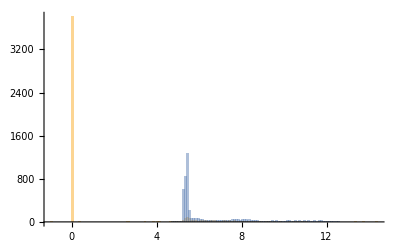
x | y | Converged | Ok | Flip | Sign | Mag | Errors | Histogram | RMSE |  | 
-Graphics- | -Graphics- | -Graphics-
320 | -Graphics-
0 | -Graphics-
3 | -Graphics-
2744 | -Graphics-
1568 | 4315 | -Graphics- | 4.24926 | -Graphics- | 6.52908
-Graphics- | -Graphics- | -Graphics-
587 | -Graphics-
0 | -Graphics-
217 | -Graphics-
2591 | -Graphics-
1240 | 4048 | -Graphics- | 3.18353 | -Graphics- | 6.12616
-Graphics- | -Graphics- | -Graphics-
554 | -Graphics-
2887 | -Graphics-
528 | -Graphics-
241 | -Graphics-
425 | 1194 | -Graphics- | 1.91214 | -Graphics- | 5.99086
-Graphics- | -Graphics- | -Graphics-
501 | -Graphics-
3159 | -Graphics-
463 | -Graphics-
183 | -Graphics-
329 | 975 | -Graphics- | 1.32474 | -Graphics- | 6.13381
-Graphics- | -Graphics- | -Graphics-
350 | -Graphics-
3591 | -Graphics-
313 | -Graphics-
133 | -Graphics-
248 | 694 | -Graphics- | 1.4475 | -Graphics- | 6.32506
-Graphics- | -Graphics- | -Graphics-
239 | -Graphics-
3882 | -Graphics-
212 | -Graphics-
111 | -Graphics-
191 | 514 | -Graphics- | 1.02821 | -Graphics- | 6.39715

```mathematica
(* Ploting all Errors and RMSE from test 1, n different scales *)
ntest=4;
d=1;
mode="Constrained";
Subscript[gridRt^mode, d][[ntest]]
```

### Constrained is the best?

```mathematica
bestScore[convergence_,rmsedef_,rmseundef_]:=Block[{},(
(rmsedef*convergence+rmseundef*4635)/(4635+convergence)
)]
```

```mathematica
ntest=3;
d=1;
```

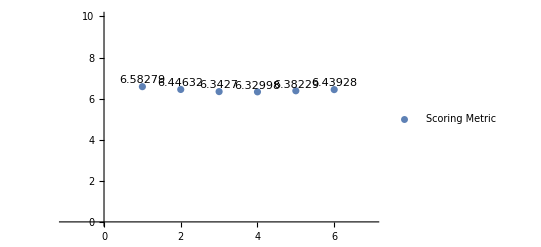

```mathematica
mode="OverConstrained";

offset={0,.6};
Show[
ListPlot[{Flatten[Subscript[resultTest^mode, d][[ntest,All,3,1,2]]/100],Subscript[resultTest^mode, d][[ntest,All,10]]},PlotLegends->{"Convergence(100)","RMSE"},PlotRange->{{-1,7},{-0,10}}],
Graphics@Text[ToString@#[[2]],#-offset]&/@Table[{n,Subscript[resultTest^mode, d][[ntest,n,10]]},{n,1,6}],
Graphics@Text[ToString@#[[2]],#+offset]&/@Table[{n,Flatten[Subscript[resultTest^mode, d][[ntest,All,3,1,2]]/100.][[n]]},{n,1,6}]
];

offset={0,.3};
Show[
ListPlot[bestScore[Flatten[Subscript[resultTest^mode, d][[ntest,All,3,1,2]]],Subscript[resultTest^mode, d][[ntest,All,10]],Subscript[resultTest^mode, d][[ntest,All,12]]],PlotLegends->{"Scoring Metric"},PlotRange->{{-1,7},{0,10}}],
Graphics@Text[ToString@#[[2]],#+offset]&/@Table[{n,bestScore[Flatten[Subscript[resultTest^mode, d][[ntest,All,3,1,2]]],Subscript[resultTest^mode, d][[ntest,All,10]],Subscript[resultTest^mode, d][[ntest,All,12]]][[n]]},{n,1,6}]
]
```

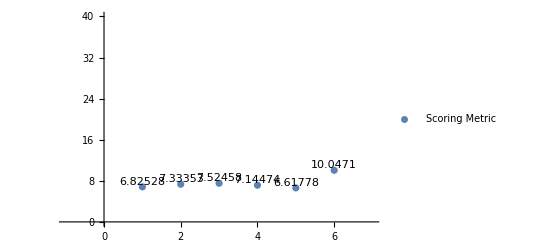

```mathematica
mode="SemiConstrained";

offset={0,.6};
Show[
ListPlot[{Flatten[Subscript[resultTest^mode, d][[ntest,All,3,1,2]]/100],Subscript[resultTest^mode, d][[ntest,All,10]]},PlotLegends->{"Convergence(100)","RMSE"},PlotRange->{{-1,7},{-0,20}}],
Graphics@Text[ToString@#[[2]],#-offset]&/@Table[{n,Subscript[resultTest^mode, d][[ntest,n,10]]},{n,1,6}],
Graphics@Text[ToString@#[[2]],#+offset]&/@Table[{n,Flatten[Subscript[resultTest^mode, d][[ntest,All,3,1,2]]/100.][[n]]},{n,1,6}]
];

offset={0,1};
Show[
ListPlot[bestScore[Flatten[Subscript[resultTest^mode, d][[ntest,All,3,1,2]]],Subscript[resultTest^mode, d][[ntest,All,10]],Subscript[resultTest^mode, d][[ntest,All,12]]],PlotLegends->{"Scoring Metric"},PlotRange->{{-1,7},{0,40}}],
Graphics@Text[ToString@#[[2]],#+offset]&/@Table[{n,bestScore[Flatten[Subscript[resultTest^mode, d][[ntest,All,3,1,2]]],Subscript[resultTest^mode, d][[ntest,All,10]],Subscript[resultTest^mode, d][[ntest,All,12]]][[n]]},{n,1,6}]
]
```

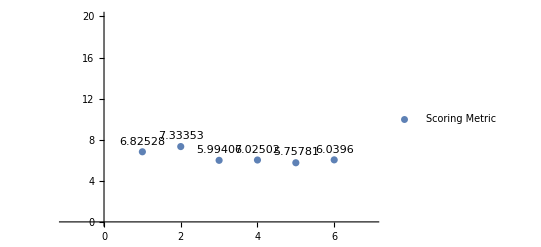

```mathematica
mode="Constrained";

offset={0,.6};
Show[
ListPlot[{Flatten[Subscript[resultTest^mode, d][[ntest,All,3,1,2]]/100],Subscript[resultTest^mode, d][[ntest,All,10]]},PlotLegends->{"Convergence(100)","RMSE"},PlotRange->{{-1,7},{-0,20}}],
Graphics@Text[ToString@#[[2]],#+offset]&/@Table[{n,Subscript[resultTest^mode, d][[ntest,n,10]]},{n,1,6}],
Graphics@Text[ToString@#[[2]],#-offset]&/@Table[{n,Flatten[Subscript[resultTest^mode, d][[ntest,All,3,1,2]]/100.][[n]]},{n,1,6}]
];

offset={0,1};
Show[
ListPlot[bestScore[Flatten[Subscript[resultTest^mode, d][[ntest,All,3,1,2]]],Subscript[resultTest^mode, d][[ntest,All,10]],Subscript[resultTest^mode, d][[ntest,All,12]]],PlotLegends->{"Scoring Metric"},PlotRange->{{-1,7},{0,20}}],
Graphics@Text[ToString@#[[2]],#+offset]&/@Table[{n,bestScore[Flatten[Subscript[resultTest^mode, d][[ntest,All,3,1,2]]],Subscript[resultTest^mode, d][[ntest,All,10]],Subscript[resultTest^mode, d][[ntest,All,12]]][[n]]},{n,1,6}]
]
```

### Density Plot Over

```mathematica
npixels=103.*45.;
d=1;
```

```mathematica
mode="OverConstrained";

rmse1=Subscript[resultTest^mode, d][[All,All,10]];
convergence1=Subscript[resultTest^mode, d][[All,All,3,1,2,1]];
density1=npixels/convergence1;

densityRes1=Flatten[{density1,rmse1},{{2,3},{1}}]

pyth[{x_,y_}]:=Sqrt[(x^2+y^2)]
magError1=pyth[#]&/@densityRes1
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{{39.9569,0.699537},{24.1406,0.783259},{26.9477,1.14582},{171.667,1.48186},{ComplexInfinity,√Mean[{}]},{ComplexInfinity,√Mean[{}]},{10.5581,5.96905},{14.4844,4.24926},{10.9834,1.64754},{34.0809,1.44977},{ComplexInfinity,√Mean[{}]},{ComplexInfinity,√Mean[{}]},{10.5581,5.96905},{21.0682,4.00532},{22.177,2.07287},{24.3947,1.15303},{28.9688,1.24876},{39.9569,0.699537},{14.4844,4.24926},{10.6064,2.05003},{11.1418,1.18143},{15.5017,1.41971},{24.1406,0.783259},{26.9477,0.700762}}

{39.963,24.1533,26.972,171.673,ComplexInfinity,ComplexInfinity,12.1286,15.0948,11.1063,34.1117,ComplexInfinity,ComplexInfinity,12.1286,21.4455,22.2737,24.422,28.9957,39.963,15.0948,10.8027,11.2043,15.5665,24.1533,26.9568}

```mathematica
mode="SemiConstrained";

rmse2=Subscript[resultTest^mode, d][[All,All,10]];
convergence2=Subscript[resultTest^mode, d][[All,All,3,1,2,1]];
density2=npixels/convergence2;

densityRes2=Flatten[{density2,rmse2},{{2,3},{1}}]

magError2=pyth[#]&/@densityRes2
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{{10.3229,4.27684},{6.9076,2.54848},{5.68712,1.99098},{28.4356,1.39266},{ComplexInfinity,√Mean[{}]},{ComplexInfinity,√Mean[{}]},{10.5581,5.96905},{14.4844,4.24926},{10.9834,1.64754},{34.0809,1.44977},{ComplexInfinity,√Mean[{}]},{ComplexInfinity,√Mean[{}]},{10.5581,5.96905},{9.49795,5.50112},{8.35135,5.24882},{8.64739,5.66839},{9.23307,3.9978},{10.3229,4.27684},{14.4844,4.24926},{7.89608,3.18353},{6.96992,2.84896},{6.69798,2.67424},{6.9076,2.54848},{8.14587,8.37045}}

{11.1738,7.36272,6.02555,28.4697,ComplexInfinity,ComplexInfinity,12.1286,15.0948,11.1063,34.1117,ComplexInfinity,ComplexInfinity,12.1286,10.976,9.86383,10.3396,10.0614,11.1738,15.0948,8.51369,7.5297,7.2121,7.36272,11.6799}

```mathematica
mode="Constrained";

rmse3=Subscript[resultTest^mode, d][[All,All,10]];
convergence3=Subscript[resultTest^mode, d][[All,All,3,1,2,1]];
density3=npixels/convergence3;

densityRes3=Flatten[{density3,rmse3},{{2,3},{1}}]

magError3=pyth[#]&/@densityRes3
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{{24.3947,1.48539},{13.2429,1.4475},{13.2429,1.40748},{59.4231,1.59743},{ComplexInfinity,√Mean[{}]},{ComplexInfinity,√Mean[{}]},{10.5581,5.96905},{14.4844,4.24926},{10.9834,1.64754},{34.0809,1.44977},{ComplexInfinity,√Mean[{}]},{ComplexInfinity,√Mean[{}]},{10.5581,5.96905},{9.49795,5.50112},{14.2178,3.56707},{15.6061,5.1884},{17.2305,1.5963},{24.3947,1.48539},{14.4844,4.24926},{7.89608,3.18353},{8.36643,1.91214},{9.2515,1.32474},{13.2429,1.4475},{19.3933,1.02821}}

{24.4399,13.3217,13.3174,59.4445,ComplexInfinity,ComplexInfinity,12.1286,15.0948,11.1063,34.1117,ComplexInfinity,ComplexInfinity,12.1286,10.976,14.6584,16.4459,17.3043,24.4399,15.0948,8.51369,8.58215,9.34586,13.3217,19.4205}

```mathematica
g1=ListPlot[{densityRes1,densityRes2,densityRes3},PlotLabel->"Density Plot",AspectRatio->1,PlotLegends->{"OverConstrained","SemiConstrained","Constrained"},ImageSize->Scaled[0.6],AxesLabel->{"Density","defined RMSE" }];
g2=ListPlot[{magError1,magError2,magError3},PlotLabel->"z = Sqrt[density^2 + RMSE^2]",PlotLegends->{"OverConstrained","SemiConstrained","Constrained"},ImageSize->Scaled[0.6],AxesLabel->{"Tests","z"}];
```

```mathematica
GraphicsGrid[{{g1,g2}},Spacings->{Scaled[-0.2],0},ImageSize->Scaled[1]]
```

-Graphics-